# 保存 A–φ 场诊断

## 缪雨轩 / Miao Yuxuan · 淮南师范学院 / Huainan Normal University

## 模型、输入与适用范围

J=−σ(jωA+∇φ); ∇·J=0

SI; exp(+j omega t); RMS; sigma=58 MS/m; mu_r=1; 20 C

读取实际保存场，复算 J、电势与规范残差，保留原场参数。

## 推导与结果解释

采用 exp(+jωt)，由原保存的 A、φ 场重构 J=−σ(jωA+∇φ)，在原输入下比较电流守恒和归一化电势、规范残差。

本入口仅改变诊断采样密度，在保存场上复算导数并与原诊断量比较可复现性，不产生新的物理场解。

原电势与规范验收仍为失败。保留网格、激励、规范及边界假设；明确一致形式并通过守恒、规范和网格研究后再推进。

```mathematica
projectRoot=NestWhile[DirectoryName,NotebookDirectory[],!FileExistsQ[FileNameJoin[{#1,"pyproject.toml"}]]&&DirectoryName[#1]=!=#1&];Get[FileNameJoin[{projectRoot,"shared","wolfram","ResearchNotebook.wl"}]];
```

## 可编辑参数

```mathematica
parameters=<|"sampling_points"->32|>;parameters
```

<|sampling_points -> 32|>

## 独立进程执行与结果

```mathematica
research=LitzNotebook`RunResearch[projectRoot,"aphi",parameters];LitzNotebook`ResearchSummary[research]
```

<|run_id -> notebook_aphi_20261014010230_0afd9871, source_model -> aphi, 
 
>   execution_status -> completed, 
 
>   physical_acceptance_status -> failed_retained_phi_gauge|>

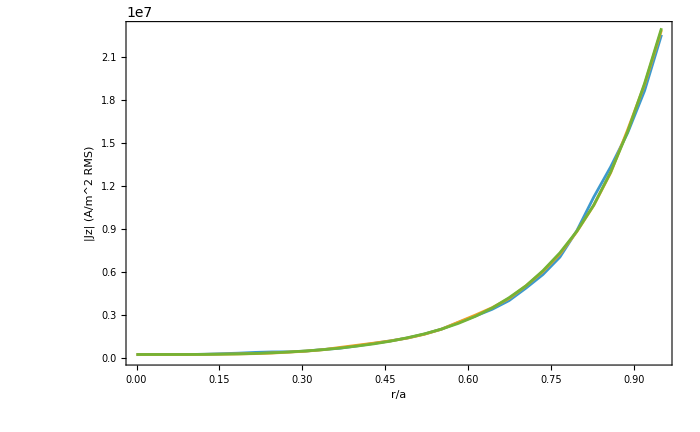

```mathematica
LitzNotebook`DisplayResearch[research]
```

## 验收与接续

核对结果中的 checks、execution_status 和 physical_acceptance_status。完整收敛与结构研究按路线 README 继续。

Sources: FEMDOC, GMRES1986; references/library.bib and references/sources.json

## 历史证据

data/evidence/v1.0.0-rc.1/; litz-research data fetch aphi